## Computation of the polynomials and its roots

Computation of the Regge polynomials from report.

```mathematica
kmax:=100;
Clear[k, d, s, pol];
P = ParallelTable[1/(n!)NorlundB[n, s+1, s+1]//Simplify,{n, 0, kmax}];
pol = ParallelTable[
2^(2k)∑_(n1=0)^k (-s)^n1(∑_(m=0)^Floor[n1/2 ] Pochhammer[s+(d-1)/2+m-k, Floor[k/2]-m]/(m!(n1-2m)!2^(2m+n1)))P[[k-n1+1]]//Simplify,
{k, 0, kmax},
Method->"FinestGrained"
]
```

Precomputed version for the first 100 polynomials.

```mathematica
Clear[d]
kmax = 100;
pol =;
```

```mathematica
Clear[polShiftNorm]
polShiftNorm = ParallelTable[pol[[k+1]]/.s->k(z+1)/.d->0//FullSimplify,{k,0,100},Method->"FinestGrained"]
```

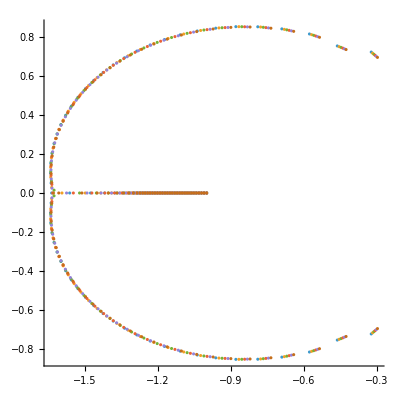

```mathematica
rootsPlot=ComplexListPlot[N[(z/. Solve[#==0,z]&/@polShiftNorm[[90;;100;;2]])],AspectRatio->1]
```

## Setting up saddle equations

Saddle equations written as functions=0 for the double integral representation of the polynomials.

```mathematica
Clear[phi,phi1,phi2,solsu,eqminus,eqplus]
phi=t/2 (z+1) (u+1)+z Log[1-u^2]-(z+1+1/k) Log[Exp[t]-1]+z Log[t];
solsu=Solve[D[phi,u]==0,u];
{phi1,phi2}=phi/.solsu
{eqminus[t_,z_,k_],eqplus[t_,z_,k_]}=D[{phi1,phi2},t]//FullSimplify
eqsq[t_,z_,k_]=eqplus[t,z,k]eqminus[t,z,k]//FullSimplify
```

{1/2 t (1+z) (1+(-2 z-√(t^2+2 t^2 z+4 z^2+t^2 z^2))/(t+t z))-(1+1/k+z) Log[-1+ⅇ^t]+z Log[t]+z Log[1-((-2 z-√(t^2+2 t^2 z+4 z^2+t^2 z^2))^2)/(t+t z)^2],1/2 t (1+z) (1+(-2 z+√(t^2+2 t^2 z+4 z^2+t^2 z^2))/(t+t z))-(1+1/k+z) Log[-1+ⅇ^t]+z Log[t]+z Log[1-((-2 z+√(t^2+2 t^2 z+4 z^2+t^2 z^2))^2)/(t+t z)^2]}

{-(t+k √(4 z^2+t^2 (1+z)^2)+t (1+k+k z) Coth[t/2])/(2 k t),-(t-k √(4 z^2+t^2 (1+z)^2)+t (1+k+k z) Coth[t/2])/(2 k t)}

1/4 (1/k^2-(4 z^2)/t^2-(1+z)^2+((1+k+k z) Coth[t/2] (2+(1+k+k z) Coth[t/2]))/k^2)

Version at 0th order in k

```mathematica
Clear[eqminusApproche,eqplusApproche,eqsqApproche]
eqminusApproche[t_,z_,k_]=Series[eqminus[t,z,k],{k,Infinity,0}]//Normal//Expand//Simplify
eqplusApproche[t_,z_,k_]=Series[eqplus[t,z,k],{k,Infinity,0}]//Normal//Expand//Simplify
eqsqApproche[t_,z_,k_]=eqplusApproche[t,z,k]eqminusApproche[t,z,k]//FullSimplify
```

-(√(4 z^2+t^2 (1+z)^2))/(2 t)-1/2 (1+z) Coth[t/2]

(√(4 z^2+t^2 (1+z)^2)-t (1+z) Coth[t/2])/(2 t)

-z^2/t^2+1/4 (1+z)^2 Csch[t/2]^2

## Visualizing the saddles in the t plane

```mathematica
θtab=Range[0,2π,π/40];
z0[θ_,r0_]:=-1+r0 Exp[I θ];
Lx=20;
Ly=20;
```

Visualisation of the position of the saddles with a black point at the position predicted by formula for the migrating saddle and the a red line at the argument predicted for the l th saddle of the tower.

```mathematica
Manipulate[theta=Pi/2-Log[Abs[ 2Pi n (1+1/z0[θtab[[l]],r0])]]/(Pi n);
{(*ComplexPlot[eqplus[t,z0[θtab[[l]],r0],kk],{t,-Lx-I Ly,Lx+I Ly},ImageSize->400],ComplexPlot[eqminus[t,z0[θtab[[l]],r0],kk],{t,-Lx-I Ly,Lx+I Ly},ImageSize->400],*)ComplexPlot[eqplus[t,z0[θtab[[l]],r0],kk]*eqminus[t,z0[θtab[[l]],r0],kk],{t,-Lx-I Ly,Lx+I Ly},ImageSize->400,Epilog->{Black,PointSize[0.02],Point[Transpose[{Re[(-z0[θtab[[l]],r0]Sqrt[kk])/Sqrt[1+z0[θtab[[l]],r0]+1/kk]],Im[(-z0[θtab[[l]],r0]Sqrt[kk])/Sqrt[1+z0[θtab[[l]],r0]+1/kk]]}]]}],Show[ComplexPlot[eqplusApproche[t,z0[θtab[[l]],r0],kk]*eqminusApproche[t,z0[θtab[[l]],r0],kk],{t,-Lx-I Ly,Lx+I Ly},ImageSize->400],ContourPlot[Arg[x+I y]-theta,{x,-Lx,Lx},{y,-Ly,Ly},Contours->{0},ContourStyle->{Thick,Red},ContourShading->None,Axes->False,Frame->False]]},{l,1,Length[θtab],1},{r0,0.3,1,0.01},{kk,10,200,10},{n,1,10,1}]
```

Structure of phi in the complex plane and on a contour around zero.

```mathematica
Manipulate[
{ComplexPlot[phi2/.z->z0[θtab[[l]],r0]/.k->kk,{t,-Lx-I Ly,Lx+I Ly},ImageSize->400]},{l,1,Length[θtab],1},{r0,0.3,1,0.01},{kk,10,200,10}]
```

```mathematica
Manipulate[
{Plot[({Re[Exp[phi2]/.z->z0[θtab[[l]],r0]/.k->kk/.t->0.01Exp[I theta]],Im[Exp[phi2]/.z->z0[θtab[[l]],r0]/.k->kk/.t->0.01Exp[I theta]]}),{theta,0,2Pi},ImageSize->400]},{l,1,Length[θtab],1},{r0,0.3,1,0.01},{kk,10,200,10}]
```

## Finding the saddles for different z points

```mathematica
ClearAll[findRootsAtZ];

(*Parameters of the root search*)
{xmin,xmax}={-10,40};
{ymin,ymax}={-100,100};

nx=200;
ny=1000;

rootTolerance=10^-8;
coalescenceThreshold=1;

xs=Subdivide[xmin,xmax,nx];
ys=Subdivide[ymin,ymax,ny];

findRootsAtZ[z_,k_,eqChosen_]:=Module[{f,vals,localMinima,seeds,roots},f[t_]:=eqChosen[t,z,k];
vals=Table[Abs[f[x+I y]],{y,ys},{x,xs}];
localMinima=Reap[Do[If[vals[[j,i]]==Min@vals[[Max[1,j-1];;Min[ny+1,j+1],Max[1,i-1];;Min[nx+1,i+1]]],Sow[xs[[i]]+I ys[[j]]]],{j,2,ny},{i,2,nx}]][[2,1]];
seeds=Select[localMinima,Abs[f[#]]<1&];
(*roots=t/.Quiet@FindRoot[f[t]==0,{t,seeds},WorkingPrecision->50];*)
roots=DeleteCases[Table[TimeConstrained[t/. Quiet@FindRoot[f[t]==0,{t,seed},WorkingPrecision->20],5,{Indeterminate}],{seed,seeds}],{Indeterminate}];
roots];
```

Finding the saddles for all the points in z plane.

```mathematica
plusGrid=ParallelTable[{-1+x Exp[I Pi y],Quiet@findRootsAtZ[-1+x Exp[I Pi y],100,eqplus]},{x,0.2,1.2,0.01},{y,-1,1,0.01}];
minusGrid=ParallelTable[{-1+x Exp[I Pi y],Quiet@findRootsAtZ[-1+x Exp[I Pi y],100,eqminus]},{x,0.2,1.2,0.01},{y,-1,1,0.01}];
```

$Aborted

$Aborted

Evaluating the action at the saddles.

```mathematica
phiPlusGrid=Flatten[plusGrid/.{a_,c_}->{a,phi2/.z->a/.k->100/.t->c},1];
phiMinusGrid=Flatten[minusGrid/.{a_,c_}->{a,phi2/.z->a/.k->100/.t->c},1];
phiGrid=ParallelTable[{phiPlusGrid[[kk,1]],Join[phiPlusGrid[[kk,2]],phiMinusGrid[[kk,2]]]},{kk,1,Length[phiPlusGrid]}]
```

Finding the Stockes lines for all of the saddles in first graph, for the dominant one on the second.

```mathematica
threshAll=0.000003;
testedGridAll=ParallelTable[{phiGrid[[kk,1]],Boole[AnyTrue[Subsets[Re[phiGrid[[kk,2]]],{2}],Abs[Subtract@@#]<threshAll&]](*Boole[Abs[Subtract@@TakeLargest[Re[phiGrid[[kk,2]]],2]]<thresh]*)},{kk,1,Length[phiPlusGrid]}];
threshBig=0.01;
testedGridBig=ParallelTable[{phiGrid[[kk,1]],(*Boole[AnyTrue[Subsets[Re[phiGrid[[kk,2]]],{2}],Abs[Subtract@@#]<thresh&]]*)Boole[Abs[Subtract@@TakeLargest[Re[phiGrid[[kk,2]]],2]]<threshBig]},{kk,1,Length[phiPlusGrid]}];
```

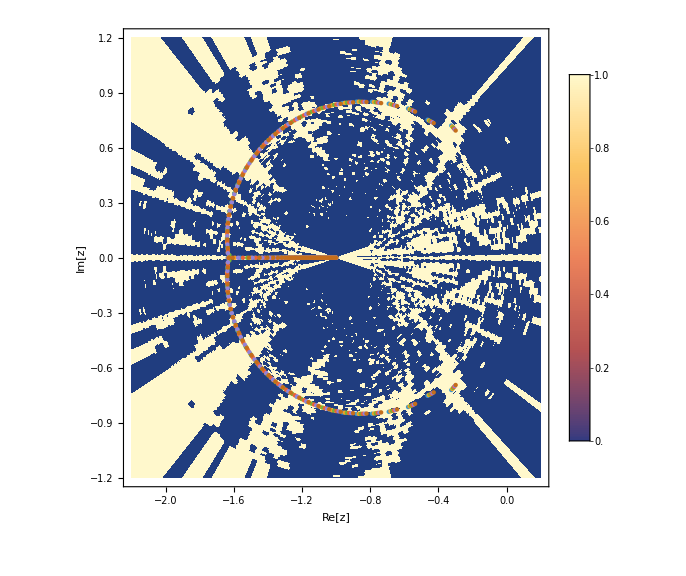
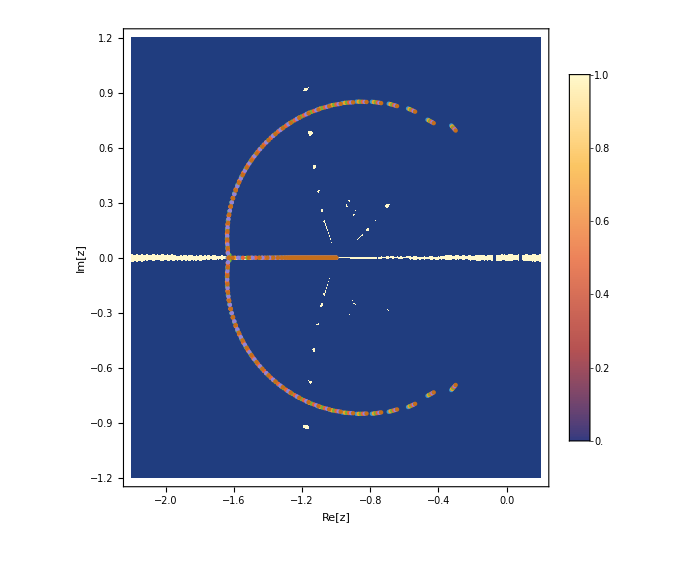

```mathematica
data1={Re[#1],Im[#1],#2}&@@@testedGridAll;
data2={Re[#1],Im[#1],#2}&@@@testedGridBig;
{Show[ListDensityPlot[data1,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{"Re[z]","Im[z]"},ImageSize->Large],rootsPlot],Show[ListDensityPlot[data2,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{"Re[z]","Im[z]"},ImageSize->Large],rootsPlot]}
```

## Semi analytical contour

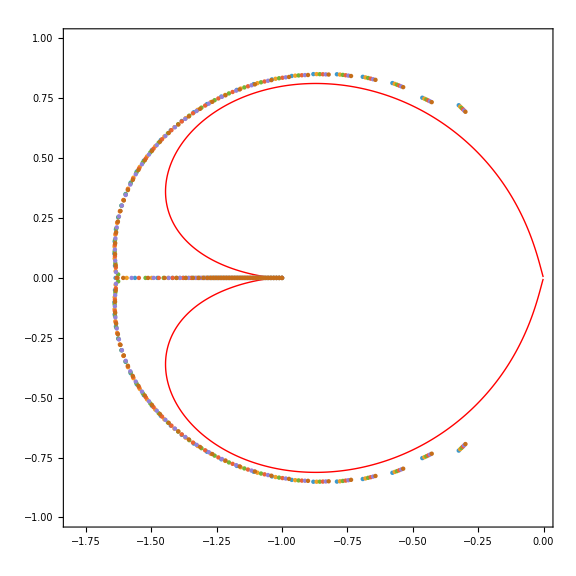

```mathematica
k=100;
n=10;

Show[ContourPlot[Arg[x+I y]-1/2 Arg[1+x+I y+1/k]+Pi/2+Log[Abs[2 Pi n (1+1/(x+I y))]]/(Pi n),{x,-1.8,0},{y,-1,1},Contours->{0},ContourShading->None,ContourStyle->{Thick,Red},PlotPoints->100,MaxRecursion->4,ImageSize->Large],ContourPlot[Arg[x+I y]-1/2 Arg[1+x+I y+1/k]-Pi/2-Log[Abs[2 Pi n (1+1/(x+I y))]]/(Pi n),{x,-1.5,0},{y,-1,1},Contours->{0},ContourShading->None,ContourStyle->{Thick,Red},PlotPoints->100,MaxRecursion->4],rootsPlot]
```